# Anyonica Package

## Installing and loading the package

## Installing the package

Download the Anyonica folder from github at: https://github.com/gert-vercleyen/Anyonica/archive/refs/heads/main.zip .

Unzip the file in a folder of choice. It doesn’t matter where you put the files since they will be copied to the correct destination automatically by Mathematica.

Open a notebook and evaluate

```mathematica
fn = CreatePacletArchive[ "pathtoanyonica" ];
PacletInstall[ fn ];
```

If you work with a mac or on linux and extracted the files in the Downloads folder, this would look like

```mathematica
fn = CreatePacletArchive[ "~/Downloads/Anyonica-main" ];
PacletInstall[ fn ];
```

If no error messages are returned the paclet was installed correctly

## Loading the Package

To load the package use the following command

```mathematica
<<Anyonica`
```

Note: the first time you load the package will take much longer because it creates data files that are optimized for import. Several loading messages of the form “Import not yet optimized for this machine. Optimizing for future use...” will be displayed. Once this is done, loading the package should be almost instantaneous in future sessions.

## All Functions

The following command returns a list of all functions that the package provides:

```mathematica
?Anyonica`*
```

Click on the function names or invoke ?<FunctionName> to get extra info on the usage of a function
Note: at this moment clicking on the FusionRing function gives some errors about formatting. This will be sorted out but is of low priority at the moment since the correct output is returned as well

```mathematica
?SolvePentagonEquations
```

```mathematica
?FusionRingAutomorphisms
```

Almost all functions have abbreviations

```mathematica
?FRA
```

## Working with fusion rings

## Initializing a FusionRing

### From a Multiplication Table

Initialize your own fusion ring by calling FusionRing with the option “Multiplicationtable” → table.

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
]
```

FR[3,1,0,_]

The format of the table is such that table[[a, b, c]] returns 𝒩_(a,b)^c, with 𝒩_(a,b)^c  the structure constants of the ring, i.e. those integers for which a×b = ∑_c 𝒩_(a,b)^c  c. The multiplication table is automatically checked for errors and specific error messages have been implemented.

Give a fusion ring one or multiple names

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"Names" -> {"Ising","SU(2)_2"}
]
```

FR[Ising]

The format of the "Names" option is a list of strings that contains the names by which this ring is known. Once a name is known the format of a fusion ring simplifies to FusionRing["name"] where "name" is the first element of the provided list of strings.

The default names for the elements are bold numbers

```mathematica
ElementNames @
FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
]
```

{𝟭,𝟮,𝟯}

Give each element its own name

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
];
ElementNames @ myring
```

{1,ψ,σ}

The names of the elements are only relevant for (the few) functions that display the elements of the ring. One of these is SymbolicMultipiclationTable (or SMT):

```mathematica
TableForm @SMT @ myring
```

1 | ψ | σ
ψ | 1 | σ
σ | σ | 1+ψ

### From the Built-In List of Fusion Rings

Access the built-in list of fusion rings

```mathematica
FusionRingList
```

{FusionRing[Trivial],FusionRing[ℤ_2],FusionRing[Fib],FusionRing[Ising],FusionRing[Rep(D_3)],FusionRing[(PSU(2))_5],28439,FusionRing[5,16,2,77],FusionRing[5,16,2,78],FusionRing[5,16,2,79],FusionRing[5,16,2,80],FusionRing[5,16,2,81],FusionRing[5,16,2,82]}
 |  |  |  |

or use the shorthand

```mathematica
FRL
```

{FusionRing[Trivial],FusionRing[ℤ_2],FusionRing[Fib],FusionRing[Ising],FusionRing[Rep(D_3)],FusionRing[(PSU(2))_5],28439,FusionRing[5,16,2,77],FusionRing[5,16,2,78],FusionRing[5,16,2,79],FusionRing[5,16,2,80],FusionRing[5,16,2,81],FusionRing[5,16,2,82]}
 |  |  |  |

One can refer to certain rings for later use

```mathematica
ring1 = FusionRingList[[4]]
```

FusionRing[Ising]

Alternatively one can use the formal code that the AnyonWiki uses to label rings. For example, the HI(ℤ_3)=FR_8^(6,2) fusion ring can be accessed using the FusionRingByCode (or FRBC) function

```mathematica
FusionRingByCode[ { 6, 2, 8 } ]
```

Note that for multiplicity-free fusion rings three numbers suffice. For rings with multiplicity a fourtuple is required. The second argument would then be the multiplicity. Rings without multiplicity can also be found using a fourtuple for which the second element equals 1:

```mathematica
FusionRingByCode[ { 6, 1, 2, 8 } ]
```

For techniques for finding rings with specific properties, see the section “Navigating the database”.

### Via Known Constructions

Generate the fusion ring ℤ_n for n=3

```mathematica
z3 = FusionRingZn[ 3 ]
```

FR[ℤ_3]

Show its multiplication table (with “fancy” formatting)

```mathematica
TableForm @ SymbolicMultiplicationTable @ z3
```

𝟭 | 𝟮 | 𝟯
𝟮 | 𝟯 | 𝟭
𝟯 | 𝟭 | 𝟮

The unit of a fusion ring is always denoted by 1. For some rings this is non-intuitive. It is, however, always  possible to rename the elements via the RenameElements function.

```mathematica
z3new = ChangeProperty[ z3, "ElementNames" -> { "0", "1", "2" } ]
```

FR[ℤ_3]

```mathematica
TableForm @ SymbolicMultiplicationTable @ z3new
```

0 | 1 | 2
1 | 2 | 0
2 | 0 | 1

Note: Always use strings as names! Using integers can confuse Mathematica at some point.

Generate the fusion ring (SU(2))_k for k=5

```mathematica
su2k5 = FusionRingSU2k[ 5 ]
```

FR[SU(2)_5]

```mathematica
TableForm @ SymbolicMultiplicationTable @ su2k5
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭+𝟯 | 𝟮+𝟰 | 𝟯+𝟱 | 𝟰+𝟲 | 𝟱
𝟯 | 𝟮+𝟰 | 𝟭+𝟯+𝟱 | 𝟮+𝟰+𝟲 | 𝟯+𝟱 | 𝟰
𝟰 | 𝟯+𝟱 | 𝟮+𝟰+𝟲 | 𝟭+𝟯+𝟱 | 𝟮+𝟰 | 𝟯
𝟱 | 𝟰+𝟲 | 𝟯+𝟱 | 𝟮+𝟰 | 𝟭+𝟯 | 𝟮
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟮 | 𝟭

Note that the order in which the elements appear differ from the same ring in the FusionRingList

```mathematica
(* Find the equivalent ring in the built-in list using the ReplaceByKnownRing function *)
su2k5FromList = ReplaceByKnownRing[ su2k5 ];
TableForm @ SymbolicMultiplicationTable @ su2k5FromList
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭+𝟯+𝟲 | 𝟮+𝟰+𝟱 | 𝟯+𝟲 | 𝟯 | 𝟮+𝟰
𝟯 | 𝟮+𝟰+𝟱 | 𝟭+𝟯+𝟲 | 𝟮+𝟰 | 𝟮 | 𝟯+𝟲
𝟰 | 𝟯+𝟲 | 𝟮+𝟰 | 𝟭+𝟯 | 𝟲 | 𝟮+𝟱
𝟱 | 𝟯 | 𝟮 | 𝟲 | 𝟭 | 𝟰
𝟲 | 𝟮+𝟰 | 𝟯+𝟲 | 𝟮+𝟱 | 𝟰 | 𝟭+𝟯

The reason for this behaviour is that for a generic ring (from the FusionRingList) there is no canonical order of the elements, while the fusion ring constructed using FusionRingSU2k is built with representation theory in mind.

Generate the fusion ring (PSU(2))_k for k=4

```mathematica
FusionRingPSU2k[ 4 ]
```

FR[PSU(2)_4]

Generate odd and even metaplectic fusion rings and compare their ranks

```mathematica
oddMeta = Table[ FusionRingSON2[ 2i +1 ], { i, 1, 5 } ]
evenMeta = Table[ FusionRingSON2[ 2i ], { i, 1, 5 } ]
Map[ Rank, oddMeta ]
Map[ Rank, evenMeta ]
```

{FR[SO(3)_2],FR[SO(5)_2],FR[SO(7)_2],FR[SO(9)_2],FR[SO(11)_2]}

{FR[SO(2)_2],FR[SO(4)_2],FR[SO(6)_2],FR[SO(8)_2],FR[SO(10)_2]}

{5,6,7,8,9}

{8,9,10,11,12}

Generate the Haagerup-Izumi ring obtained from ℤ_3

```mathematica
FusionRingHI[ CyclicGroup[3] ]
```

FR[6,1,2,_]

Any Abelian group with available multiplication table built into Mathematica (see  guide/GroupTheory in the documentation centre) can be used

```mathematica
FusionRingHI[ AbelianGroup[{3,2}] ]
```

FR[12,1,4,_]

Generate a fusion ring from a built-in group whose multiplication table is available

```mathematica
FusionRingFromGroup[ DihedralGroup[ 3 ] ]
```

FR[D_3]

```mathematica
FusionRingFromGroup[ AlternatingGroup[ 4 ] ]
```

FusionRingFromGroup[AlternatingGroup[4]]

Generate the Tambara-Yamagami fusion ring of a group

```mathematica
FusionRingTY[ DihedralGroup[2] ]
```

FR[5,1,0,_]

Generate character rings of finite groups

```mathematica
FusionRingRepG[ SymmetricGroup[4] ]
```

The function FusionRingRepG can take a built-in group, a group name (as a string), or a couple { groupName, n } as argument. For the valid group names and couples, see the documentation on FiniteGroupData.

Check that the Quaternion group and D_4 have the same character table

```mathematica
EquivalentFusionRingsQ[
	FusionRingRepG[ DihedralGroup[4] ],
	FusionRingRepG[ "Quaternion" ]
]
```

True

## Properties of Fusion Rings

Each fusion ring contains stored standard data.  The full structure of a FusionRing object is rather involved, though:

```mathematica
FullForm @ FusionRingList[[17]]
```

FusionRing[Association[Rule["Barcode",9520970329946264247],Rule["DirectProductDecompositions",Hold[List[]]],Rule["Dual",Association[Rule[1,1],Rule[2,2],Rule[3,4],Rule[4,3]]],Rule["ElementNames",List["\|01D7ED","\|01D7EE","\|01D7EF","\|01D7F0"]],Rule["ElementsName",None],Rule["FormalParameters",List[4,1,2,4]],Rule["MultiplicationTable",List[List[List[1,0,0,0],List[0,1,0,0],List[0,0,1,0],List[0,0,0,1]],List[List[0,1,0,0],List[1,0,0,0],List[0,0,0,1],List[0,0,1,0]],List[List[0,0,1,0],List[0,0,0,1],List[0,1,1,1],List[1,0,1,1]],List[List[0,0,0,1],List[0,0,1,0],List[1,0,1,1],List[0,1,1,1]]]],Rule["Names",List["Pseudo PSU(2)_6","[I ⊴ ℤ_2]"]],Rule["SubFusionRings",Hold[List[List[List[1,2],FRBC[List[2,1,0,1]]]]]],Rule["QuantumDimensions",List[1,1,Plus[1,Power[2,Rational[1,2]]],Plus[1,Power[2,Rational[1,2]]]]],Rule["SMatrices",List[]],Rule["TwistFactors",List[List[0,0,0,0],List[0,0,Rational[1,2],Rational[1,2]]]],Rule["ModularData",List[]],Rule["Characters",List[List[1,1,Plus[1,Power[2,Rational[1,2]]],Plus[1,Power[2,Rational[1,2]]]],List[1,1,Plus[1,Times[-1,Power[2,Rational[1,2]]]],Plus[1,Times[-1,Power[2,Rational[1,2]]]]],List[1,-1,Complex[0,1],Complex[0,-1]],List[1,-1,Complex[0,-1],Complex[0,1]]]]]]

To get information about the various saved properties of a fusion ring it is better to use the built-in functions designed for this job.

Note: while it is technically possible to access the data of a fusion ring by using the ring[“property”] syntax, it is safer not to do so. For example, the names of the properties could be misleading because of legacy reasons. 
In any case one should never assign values using ring[“property”] = value! Doing this skips sanity checks and can have unwanted side effects. Always use the ChangeProperty function for manually setting values of fusion rings.

Get the number of generators of a fusion ring

```mathematica
r = FusionRingList[[15]];
Rank[ r ]
```

4

Get the multiplication table of a fusion ring

```mathematica
MultiplicationTable[ r ] (* or MT[ r ] *)
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,1,1},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}},{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,1,0}}}

Get the common names of a fusion ring

```mathematica
Names[ r ]
```

{Potts,TY(ℤ_3),[ℤ_3 ⊴ ℤ_3]}

Get the names of  the elements of a fusion ring

```mathematica
ElementNames[ r ]
```

{𝟭,𝟮,𝟯,𝟰}

Get the symbolic multiplication table of a fusion ring

```mathematica
SymbolicMultiplicationTable[ r ] (* or SMT[ r ] *)
```

{{𝟭,𝟮,𝟯,𝟰},{𝟮,𝟭+𝟯+𝟰,𝟮,𝟮},{𝟯,𝟮,𝟰,𝟭},{𝟰,𝟮,𝟭,𝟯}}

Use TableForm to get a nice overview

```mathematica
TableForm[ SMT[ r ] ]
```

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟯+𝟰 | 𝟮 | 𝟮
𝟯 | 𝟮 | 𝟰 | 𝟭
𝟰 | 𝟮 | 𝟭 | 𝟯

Get the matrix that sends each particle to its antiparticle

```mathematica
AntiparticleMatrix[ r ] (* or AM[ r ] *)
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

It is clear that the first two elements are self dual and the last two are each others antiparticle

```mathematica
MatrixForm[ AM[ r ] ]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Find the multiplicity  of a fusion ring

```mathematica
Multiplicity[ r ] (* Or Mult[ r ] *)
```

1

Check whether a fusion ring is commutative

```mathematica
CommutativeQ[ r ] (* Or CQ[ r ] *)
```

True

Check whether a fusion ring comes from a group

```mathematica
GroupQ[ r ] (* Or GQ[ r ] *)
```

False

Get the indices of the non-zero structure constants 𝒩_(a,b)^c ≠ 0

```mathematica
NonZeroStructureConstants[ r ] (* or NZSC[ r ] *)
```

{{1,1,1},{1,2,2},{1,3,3},{1,4,4},{2,1,2},{2,2,1},{2,2,3},{2,2,4},{2,3,2},{2,4,2},{3,1,3},{3,2,2},{3,3,4},{3,4,1},{4,1,4},{4,2,2},{4,3,1},{4,4,3}}

Get the number of nonzero structure constants

```mathematica
NNonZeroStructureConstants[ r ] (* or NNZSC[ r ] *)
```

18

Get a tuple with the number of self-dual and non-self-dual elements

```mathematica
NSelfDualNonSelfDual[ r ] (* or NSDNSD[ r ] *)
```

{2,2}

Functions for each number separately are also available

```mathematica
{ NSelfDual[ r ], NNonSelfDual[ r ] } (* or { NSD[ r ], NNSD[ r ] } *)
```

{2,2}

Get the Frobenius-Perron dimensions of the elements, in the same order as the elements

```mathematica
FrobeniusPerronDimensions[ r ] (* or FPDims[ r ] *)
```

{1,√3,1,1}

Get the  Frobenius-Perron dimension of the ring

```mathematica
FrobeniusPerronDimension[ r ] (* or FPDim[ r ] *)
```

6

Get the formal code of the fusion ring

```mathematica
FormalCode[ r ] (* or FC[ r ] *)
```

{4,1,2,2}

This code can then be used to quickly  search for the fusion ring in the database

```mathematica
FusionRingByCode[{4,1,2,2}]
```

FR[Potts]

For multiplicity-free fusion rings one can omit the second number (= the multiplicity)

```mathematica
FusionRingByCode[{4,2,2}]
```

FR[Potts]

To get the modular data of a fusion ring, invoke

```mathematica
r = FRL[[20]];
ModularData[ r ] (* or SM[ r ] *)
```

{<|SMatrix→{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,1/2,-1/2},{1/2,-1/2,0,-1/2,1/2}},TwistFactors→{{0,0,-1/3,3/8,-1/8},{0,0,-1/3,-1/8,3/8},{0,0,1/3,1/8,-3/8},{0,0,1/3,-3/8,1/8}}|>,<|SMatrix→{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,-1/2,1/2},{1/2,-1/2,0,1/2,-1/2}},TwistFactors→{{0,0,1/3,-1/8,3/8},{0,0,1/3,3/8,-1/8},{0,0,-1/3,-3/8,1/8},{0,0,-1/3,1/8,-3/8}}|>}

The output is a list of associations. Each association contains an S-matrix and a list of compatible twist factors.  
To retrieve the projective representations one can evaluate the following code

```mathematica
reps = 
Table[
	Table[
		{ asso["SMatrix"], DiagonalMatrix[ Exp[ 2 Pi I asso["TwistFactors"][[i]] ] ] },
		{ i, Length[ asso["TwistFactors"] ] }
	],
	{ asso, ModularData[ r ] }
];

TableForm[ Map[ MatrixForm, reps, {3} ], TableDepth->2, TableDirections->Row ]
```

{(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | 1/2 | -1/2
1/2 | -1/2 | 0 | -1/2 | 1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4))} | {(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | -1/2 | 1/2
1/2 | -1/2 | 0 | 1/2 | -1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((3 ⅈ π)/4))}
{(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | 1/2 | -1/2
1/2 | -1/2 | 0 | -1/2 | 1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((3 ⅈ π)/4))} | {(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | -1/2 | 1/2
1/2 | -1/2 | 0 | 1/2 | -1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4))}
{(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | 1/2 | -1/2
1/2 | -1/2 | 0 | -1/2 | 1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4))} | {(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | -1/2 | 1/2
1/2 | -1/2 | 0 | 1/2 | -1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4))}
{(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | 1/2 | -1/2
1/2 | -1/2 | 0 | -1/2 | 1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4))} | {(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | -1/2 | 1/2
1/2 | -1/2 | 0 | 1/2 | -1/2),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4))}

Notes: 
1. The S-matrices are normalized to be unitary. This is not the case for S-matrices of the fusion categories. 
2. The S-matrices and twist factors are calculated using only data from the fusion ring. It might be that only few combinations of S-matrices and twist factors appear as modular data of the fusion category.   
3. Functions such as TableForm and MatrixForm don’t just display the results nicely, they actually create formatted objects that can not be used as matrices in the usual sense! You might want to use these functions only after you’re done calculating and/or assigning values.

Having modular data does not imply the fusion ring has a modular category. For example, the ring FR_11^(7,2) has modular data but is not categorifiable .

```mathematica
ModularData @ FRBC @ {7,2,11}
FusionCategories @ FRBC @ {7,2,11}
```

{<|SMatrix→{{Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,1/2,1/(2 √2),1/(2 √2)},{Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,-1/2,-1/(2 √2),-1/(2 √2)},{Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,1/2,-1/(2 √2),-1/(2 √2)},{Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,-1/2,1/(2 √2),1/(2 √2)},{1/2,-1/2,1/2,-1/2,0,0,0},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),0,-ⅈ/2,ⅈ/2},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),0,ⅈ/2,-ⅈ/2}},TwistFactors→{{0,1/2,1/4,-1/4,-11/32,1/32,1/32},{0,1/2,-1/4,1/4,-13/32,7/32,7/32},{0,1/2,1/4,-1/4,5/32,-15/32,-15/32},{0,1/2,-1/4,1/4,3/32,-9/32,-9/32}}|>,<|SMatrix→{{Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,1/2,1/(2 √2),1/(2 √2)},{Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.191Root[1-32 #1^2+128 #1^4&,3]0.1913417161825449,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,-1/2,-1/(2 √2),-1/(2 √2)},{Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,1/2,-1/(2 √2),-1/(2 √2)},{Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root0.462Root[1-32 #1^2+128 #1^4&,4]0.4619397662556434,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,Root-0.191Root[1-32 #1^2+128 #1^4&,2]-0.1913417161825449,-1/2,1/(2 √2),1/(2 √2)},{1/2,-1/2,1/2,-1/2,0,0,0},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),0,ⅈ/2,-ⅈ/2},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),0,-ⅈ/2,ⅈ/2}},TwistFactors→{{0,1/2,1/4,-1/4,-3/32,9/32,9/32},{0,1/2,-1/4,1/4,-5/32,15/32,15/32},{0,1/2,1/4,-1/4,13/32,-7/32,-7/32},{0,1/2,-1/4,1/4,11/32,-1/32,-1/32}}|>}

{}

Note: the empty list as output of the FusionCategories function can also mean that the data is not available in the package. For all multiplicity-free fusion rings up to rank 7 this data is available, though, and therefore and empty list for such a fusion ring implies that the ring is not categorifiable.

Having modular data does not imply that the fusion category is unitary. If the first row of the S-matrix is never positive then any categorification must be non-unitary. Possible examples of such rings can be found using the following code

```mathematica
positiveFirstRowQ[ mat_ ] := And @@ Thread[ mat[[1]] > 0 ];

nonPosModularSMatQ[ modularData_ ] := And @@ Table[ Not @ positiveFirstRowQ @ tuple["SMatrix"], { tuple, modularData } ];

nonPosModularRingQ[ ring_ ] := 
	With[ { md = ModularData[ring] },
		md =!= {} && nonPosModularSMatQ[ModularData[ring]]
	];
	
nonPosModularRings = Select[ FRL, nonPosModularRingQ ]
```

{FR[6,2,0,94]}

Get the symbolic characters of a fusion ring

```mathematica
FusionRingCharacters[ r ] (* or FRC *)
```

{{1,1,2,√3,√3},{1,1,2,-√3,-√3},{1,1,-1,0,0},{1,-1,0,1,-1},{1,-1,0,-1,1}}

Not all fusion rings have symbolic characters. In that case the numeric characters are returned

```mathematica
r = FusionRingByCode[{7,1,4,6}]
FRC[ r ]
```

FR[7,1,4,6]

{{1.,4.2044,3.49086,1.,1.,3.49086,3.49086},{1.,-1.56885,0.34338,1.,1.,0.34338,0.34338},{1.+0. ⅈ,0.,-1.61803+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,0.809017+1.40126 ⅈ,0.809017-1.40126 ⅈ},{1.+0. ⅈ,0.,-1.61803+0. ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,0.809017-1.40126 ⅈ,0.809017+1.40126 ⅈ},{1.,1.36445,-0.834243,1.,1.,-0.834243,-0.834243},{1.,0.,0.618034+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ},{1.,0.,0.618034+0. ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.309017+0.535233 ⅈ,-0.309017-0.535233 ⅈ}}

## Operations on Fusion Rings

Permute the generators of a ring.

```mathematica
r = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
];
rPermuted = PermutedRing[ r, {1, 3, 2} ];

TableForm @ SMT @ r
TableForm @ SMT @ rPermuted
```

1 | ψ | σ
ψ | 1 | σ
σ | σ | 1+ψ

1 | ψ | σ
ψ | 1+σ | ψ
σ | ψ | 1

Note that the names of the elements remain the same.

The first element should always be the unit element and can therefore be omitted in the permutation vector

```mathematica
TableForm @ SMT @ PermutedRing[ r, { 3, 2 } ]
```

1 | ψ | σ
ψ | 1+σ | ψ
σ | ψ | 1

Rename the elements of a ring

```mathematica
ElementNames @ r
ElementNames @ ChangeProperty[ r, "ElementNames" ->  { "0", "1", "2" } ]
```

{1,ψ,σ}

{0,1,2}

Sort the elements in a ring with respect to quantum dimensions of elements

```mathematica
r = PermutedRing[ FusionRingList[[13]], {1,3,2,4} ];
TableForm @ SMT @ r 
TableForm @ SMT @ SortedRing[ r ]
```

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟮+𝟯+𝟰 | 𝟮+𝟰 | 𝟮+𝟯+𝟰
𝟯 | 𝟮+𝟰 | 𝟭+𝟰 | 𝟮+𝟯
𝟰 | 𝟮+𝟯+𝟰 | 𝟮+𝟯 | 𝟭+𝟮+𝟰

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟯 | 𝟮+𝟰 | 𝟯+𝟰
𝟯 | 𝟮+𝟰 | 𝟭+𝟯+𝟰 | 𝟮+𝟯+𝟰
𝟰 | 𝟯+𝟰 | 𝟮+𝟯+𝟰 | 𝟭+𝟮+𝟯+𝟰

Sort the elements in a ring on duality an then with respect to quantum dimensions of elements

```mathematica
r = FusionRingList[[ 58 ]];
TableForm @ SMT @ r
TableForm @ SMT @ SortedRing[ r, "SortBy" -> "Selfdual-Conjugates" ]
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭 | 𝟯 | 𝟰 | 𝟲 | 𝟱
𝟯 | 𝟯 | 𝟭+𝟮+𝟯+𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟰 | 𝟰
𝟰 | 𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟭+𝟮+𝟯+𝟰 | 𝟯 | 𝟯
𝟱 | 𝟲 | 𝟰 | 𝟯 | 𝟮 | 𝟭
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟭 | 𝟮

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭 | 𝟯 | 𝟰 | 𝟲 | 𝟱
𝟯 | 𝟯 | 𝟭+𝟮+𝟯+𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟰 | 𝟰
𝟰 | 𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟭+𝟮+𝟯+𝟰 | 𝟯 | 𝟯
𝟱 | 𝟲 | 𝟰 | 𝟯 | 𝟮 | 𝟭
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟭 | 𝟮

Add one or multiple names to a fusion ring

```mathematica
r1 = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
]
r2 = ChangeProperty[ r1, "Names" -> {"Ising"} ]
r2 = ChangeProperty[ r2, "Names" -> Join[ Names @ r2, {"SU(2)_2"} ] ]
Names @ r2
```

FR[3,1,0,_]

FR[Ising]

FR[Ising]

{Ising,SU(2)_2}

Any of the standard options for the FusionRing function can be changed via the ChangeProperty function.

```mathematica
Options[FusionRing][[;;,1]]
```

{MultiplicationTable,Names,ElementsName,ElementNames,Barcode,FormalParameters,DirectProductDecompositions,SubFusionRings,QuantumDimensions,SMatrices,TwistFactors,ModularData,Characters}

Note: Not all data is checked for consistency when changing properties.

## Combining, Decomposing, and Comparing Fusion Rings

Take a tensor product of fusion rings

```mathematica
r1 = FusionRingList[[4]]
r2 = FusionRingList[[3]]
prodring = TensorProduct[r1,r2]
TableForm @ SMT @ prodring
```

FR[Ising]

FR[Fib]

FR[6,1,0,_]

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭+𝟮 | 𝟰 | 𝟯+𝟰 | 𝟲 | 𝟱+𝟲
𝟯 | 𝟰 | 𝟭 | 𝟮 | 𝟱 | 𝟲
𝟰 | 𝟯+𝟰 | 𝟮 | 𝟭+𝟮 | 𝟲 | 𝟱+𝟲
𝟱 | 𝟲 | 𝟱 | 𝟲 | 𝟭+𝟯 | 𝟮+𝟰
𝟲 | 𝟱+𝟲 | 𝟲 | 𝟱+𝟲 | 𝟮+𝟰 | 𝟭+𝟮+𝟯+𝟰

The tensor product of fusion rings is associative and TensorProduct can take any number of rings

```mathematica
r1 = FusionRingList[[4]];
r2 = FusionRingList[[3]];
r3 = FusionRingList[[5]];

prodring1 = TensorProduct[ TensorProduct[ r1, r2 ], r3 ];
prodring2 = TensorProduct[ r1, TensorProduct[ r2, r3 ] ];
prodring3 = TensorProduct[ r1, r2, r3 ];

prodring1 == prodring2 == prodring3
```

True

Decompose a ring as a tensor product of smaller rings

```mathematica
r = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{1,0,0,1,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,1,0,1,0},{0,1,0,0,0,1},{1,0,0,1,0,0}},
		{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,1,0,0,0,1},{1,0,0,1,0,0},{0,0,1,0,1,0}}
		}
];
WhichDecompositions[ r ]
```

{{FR[Fib],FR[ℤ_3]}}

Check whether two fusion rings are the same up to permutation of the generators

```mathematica
r1 = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{1,0,0,1,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,1,0,1,0},{0,1,0,0,0,1},{1,0,0,1,0,0}},
		{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,1,0,0,0,1},{1,0,0,1,0,0},{0,0,1,0,1,0}}
		}
];
r2 = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,1,0,0,0,1},{0,0,1,1,0,0},{1,0,0,0,1,0}},
		{{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,1,0,0},{1,0,0,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0},{1,0,0,0,1,0},{0,1,0,0,0,1},{0,0,1,1,0,0}}
		}
];

EquivalentFusionRingsQ[ r1, r2 ]
```

True

Find out which permutation relates two fusion rings

```mathematica
perm = WhichPermutation[ r1, r2 ]
```

{1,2,3,5,4,6}

This implies that the following equality holds

```mathematica
MultiplicationTable[r1][[perm,perm,perm]] == MultiplicationTable[r2]
```

True

Find all sub-fusion rings of a fusion ring

```mathematica
r = FRL[[20]];
SubFusionRings[ r ] (* or SFR *)
```

{{{1,2},FR[ℤ_2]},{{1,2,3},FR[Rep(D_3)]}}

The result tells us that elements 1 and 2 constitute have a ℤ_2 structure and elements 1, 2, and 3 have a Rep(D_3) structure.

Find the upper central series and adjoint of a fusion ring

```mathematica
UpperCentralSeries[r]
AdjointFusionRing[r]
```

{{{1,2,3,4,5},FR[SU(2)_4]},{{1,2,3},FR[Rep(D_3)]}}

{{1,2,3},FR[Rep(D_3)]}

Find out whether a fusion ring is nilpotent

```mathematica
NilpotentFusionRingQ[r]
```

Find the universal grading of a fusion ring

```mathematica
UniversalGrading[r]
```

Find the commutator  of a sub fusion ring

```mathematica
FusionRingCommutator[ r, SubFusionRings[r][[2]] ]
```

{{1,2,3,4,5},FR[SU(2)_4]}

Note: For some functions the specific embedding of the subring is necessary so a couple consisting of (1) a list containing the elements of the bigger ring and (2) the subring is required. The function SubFusionRingQ does not require the embedding since it searches for one itself.

## Navigating the Database

### Finding rings by properties

The package comes with a table of fusion rings

```mathematica
FusionRingList (* or FRL *)
```

To search for rings with certain properties the function Cases is useful,

```mathematica
?Cases
```

especially when combined with the /; (Condition) construct

```mathematica
?Condition
```

Finding all fusion rings for which a property p holds is done using Cases[ FRL, ring_/; p[ring]  ] but of course multiple properties can be combined using the && and || operators.

Search for all multiplicity-free fusion rings of rank 4

```mathematica
multFree4ParticleRings = Cases[ FRL, ring_/; Rank[ring] == 4 && Mult[ring] == 1 ]
```

{FR[ℤ_2×ℤ_2],FR[SU(2)_3],FR[Rep(D_5)],FR[PSU(2)_6],FR[Fib×Fib],FR[PSU(2)_7],FR[ℤ_4],FR[Potts],FR[Fib(ℤ_3)],FR[Pseudo PSU(2)_6]}

If any of these are of special interest you can use their unique 4-digit codes for later reference

```mathematica
FormalCode /@ multFree4ParticleRings
FusionRingByCode[ { 4, 1, 0, 4 } ]
```

{{4,1,0,1},{4,1,0,2},{4,1,0,3},{4,1,0,4},{4,1,0,5},{4,1,0,6},{4,1,2,1},{4,1,2,2},{4,1,2,3},{4,1,2,4}}

FR[PSU(2)_6]

Search for all fusion rings of rank 6 that are not commutative

```mathematica
Cases[ FRL, ring_/; Rank[ ring ] == 6 && Not[ CommutativeQ[ ring ] ] ]
```

{FR[D_3],FR[HI(ℤ_3)],FR[6,2,2,1],FR[6,2,2,33],FR[6,3,2,11],FR[6,4,2,43],FR[6,5,2,73],FR[6,6,2,140],FR[6,6,2,312],FR[6,7,2,115],FR[6,7,2,179],FR[6,8,2,48],FR[6,8,2,338]}

Search for all multiplicity-free fusion rings with Frobenius-Perron  dimension between 9 and 16

```mathematica
Cases[ FRL, ring_/; Mult[ring] == 1 && 9 < FPDim[ring] < 16 ]
```

{FR[(PSU(2))_5],FR[Rep(D_5)],FR[PSU(2)_6],FR[Fib×Fib],FR[Pseudo PSU(2)_6],FR[Fib(ℤ_2×ℤ_2)],FR[SU(2)_4],FR[Rep(D_7)],FR[Fib(ℤ_4)],FR[Pseudo SU(2)_4],FR[ℤ_2×Rep(D_3)],FR[TriCritIsing],FR[Rep(Dic_12)],FR[TY(ℤ_5)],FR[[ℤ_5 ⊴ ℤ_5]],FR[Fib×ℤ_3],FR[TY(D_3)],FR[[D_3 ⊴ D_3]],FR[TY(ℤ_2×ℤ_3)],FR[[ℤ_6 ⊴ ℤ_6]],FR[Fib×ℤ_2×ℤ_2],FR[[ℤ_3 ⊴ D_3]],FR[[ℤ_3 ⊴ D_3]],FR[ℤ_2×Potts],FR[Fib×ℤ_4],FR[TY(ℤ_7)],FR[[ℤ_3 ⊴ ℤ_6]],FR[[ℤ_2 ⊴ ℤ_6]],FR[Ising×ℤ_3]}

Search for all fusion rings that are a tensor product of smaller fusion rings

```mathematica
Cases[ FRL, ring_/; WhichDecompositions[ ring ] ≠ {} ]
```

{FR[ℤ_2×ℤ_2],FR[SU(2)_3],FR[Fib×Fib],FR[ℤ_2×Ising],FR[ℤ_2×Rep(D_3)],FR[TriCritIsing],FR[Fib×Rep(D_3)],FR[SU(2)_5],FR[Fib×(PSU(2))_5],FR[ℤ_6],FR[Fib×ℤ_3],FR[ℤ_2×ℤ_2×ℤ_2],FR[Fib×ℤ_2×ℤ_2],FR[Rep(D_5)×ℤ_2],FR[PSU(2)_6×ℤ_2],FR[Fib×Fib×ℤ_2],FR[Fib×(Rep(D)_5)],FR[(SU(2))_7],FR[Fib×(PSU(2))_6],FR[Fib×Fib×Fib],FR[Fib×(PSU(2))_7],FR[ℤ_2×ℤ_4],FR[ℤ_2×Potts],FR[ℤ_2×Fib(ℤ_3)],FR[Fib×ℤ_4],FR[Fib×Potts],FR[Fib×Fib(ℤ_3)],FR[ℤ_2×(Peudo (PSU(2))_6)],FR[Fib×(Peudo (PSU(2))_6)],FR[Ising×Ising],FR[Ising×Rep(D_3)],FR[Rep(D_3)×Rep(D_3)],FR[Ising×(PSU(2))_5],FR[Rep(D_3)×(PSU(2))_5],FR[(PSU(2))_5×(PSU(2))_5],FR[Ising×ℤ_3],FR[Rep(D_3)×ℤ_3],FR[(PSU(2))_5×ℤ_3],FR[ℤ_3×ℤ_3],FR[4,2,0,1],FR[4,2,0,8],FR[6,2,0,2],FR[6,2,0,4],FR[6,2,0,9],FR[6,2,0,16],FR[6,2,0,22],FR[6,2,0,28],FR[6,2,0,29],FR[6,2,0,34],FR[6,2,0,41],FR[6,2,4,2],FR[8,2,0,3],FR[8,2,0,4],FR[8,2,0,21],FR[8,2,0,22],FR[8,2,0,23],FR[8,2,0,33],FR[8,2,0,54],FR[8,2,0,55],FR[8,2,0,58],FR[8,2,0,59],FR[8,2,0,69],FR[8,2,0,75],FR[8,2,0,76],FR[8,2,0,77],FR[8,2,0,85],FR[8,2,0,91],FR[8,2,0,92],FR[8,2,0,103],FR[8,2,0,106],FR[8,2,0,115],FR[8,2,0,116],FR[8,2,0,123],FR[8,2,0,124],FR[8,2,0,125],FR[8,2,0,131],FR[8,2,0,144],FR[8,2,0,159],FR[8,2,0,181],FR[8,2,0,182],FR[8,2,0,189],FR[8,2,0,203],FR[8,2,0,265],FR[8,2,4,2],FR[8,2,4,6],FR[8,2,4,22],FR[8,2,4,26],FR[8,2,4,39],FR[8,2,4,46],FR[8,2,4,67],FR[8,2,4,81],FR[4,3,0,5],FR[4,3,0,15],FR[6,3,0,8],FR[6,3,0,34],FR[6,3,0,49],FR[6,3,0,50],FR[6,3,0,59],FR[6,3,0,66],FR[6,3,0,96],FR[6,3,0,128],FR[6,3,0,135],FR[6,3,0,136],FR[6,3,0,167],FR[6,3,4,4],FR[4,4,0,17],FR[4,4,0,22],FR[4,4,0,34],FR[6,4,0,34],FR[6,4,0,35],FR[6,4,0,197],FR[6,4,0,198],FR[6,4,0,235],FR[6,4,0,236],FR[6,4,0,237],FR[6,4,0,260],FR[6,4,0,274],FR[6,4,0,279],FR[6,4,0,296],FR[6,4,0,363],FR[6,4,0,377],FR[6,4,0,461],FR[6,4,0,475],FR[6,4,0,476],FR[6,4,0,477],FR[6,4,0,551],FR[6,4,4,8],FR[4,5,0,23],FR[4,5,0,44],FR[6,5,0,1],FR[6,5,0,5],FR[6,5,0,77],FR[6,5,0,78],FR[6,5,0,102],FR[6,5,0,103],FR[6,5,0,124],FR[6,5,0,214],FR[6,5,0,216],FR[6,5,0,217],FR[6,5,4,7],FR[4,6,0,44],FR[4,6,0,54],FR[4,6,0,69],FR[6,6,0,1],FR[6,6,0,2],FR[6,6,0,3],FR[6,6,0,15],FR[6,6,0,136],FR[6,6,0,148],FR[6,6,0,200],FR[6,6,0,201],FR[6,6,0,202],FR[6,6,0,204],FR[6,6,0,231],FR[6,6,0,232],FR[6,6,0,290],FR[6,6,0,305],FR[6,6,0,335],FR[6,6,0,336],FR[6,6,0,337],FR[6,6,0,339],FR[6,6,0,356],FR[6,6,0,394],FR[6,6,0,419],FR[6,6,0,424],FR[6,6,0,425],FR[6,6,0,461],FR[6,6,4,13],FR[4,7,0,52],FR[4,7,0,77],FR[6,7,0,5],FR[6,7,0,6],FR[6,7,0,14],FR[6,7,0,252],FR[6,7,0,253],FR[6,7,0,254],FR[6,7,0,289],FR[6,7,0,290],FR[6,7,0,344],FR[6,7,0,472],FR[6,7,0,476],FR[6,7,0,477],FR[6,7,4,11],FR[4,8,0,87],FR[4,8,0,102],FR[4,8,0,124],FR[6,8,0,13],FR[6,8,0,14],FR[6,8,0,15],FR[6,8,0,16],FR[6,8,0,29],FR[6,8,0,55],FR[6,8,0,405],FR[6,8,0,406],FR[6,8,0,541],FR[6,8,0,542],FR[6,8,0,546],FR[6,8,0,547],FR[6,8,0,548],FR[6,8,0,561],FR[6,8,0,625],FR[6,8,0,626],FR[6,8,0,627],FR[6,8,0,726],FR[6,8,0,746],FR[6,8,0,791],FR[6,8,0,792],FR[6,8,0,793],FR[6,8,0,879],FR[6,8,0,940],FR[6,8,0,942],FR[6,8,0,943],FR[6,8,0,944],FR[6,8,4,16],FR[4,9,0,103],FR[4,9,0,121],FR[4,9,0,142],FR[4,10,0,130],FR[4,10,0,150],FR[4,10,0,172],FR[4,11,0,174],FR[4,11,0,228],FR[4,12,0,227],FR[4,12,0,245],FR[4,12,0,247],FR[4,12,0,274],FR[4,13,0,180],FR[4,13,0,233],FR[4,14,0,265],FR[4,14,0,295],FR[4,14,0,334],FR[4,15,0,276],FR[4,15,0,305],FR[4,15,0,336],FR[4,16,0,443],FR[4,16,0,475],FR[4,16,0,481],FR[4,16,0,509]}

Search for all fusion rings of which Anyonica knows its common name

```mathematica
Cases[ FRL, ring_/; Names[ ring ] ≠ {} ]
```

{FR[Trivial],FR[ℤ_2],FR[Fib],FR[Ising],FR[Rep(D_3)],FR[(PSU(2))_5],FR[ℤ_3],FR[ℤ_2×ℤ_2],FR[SU(2)_3],FR[Rep(D_5)],FR[PSU(2)_6],FR[Fib×Fib],FR[PSU(2)_7],FR[ℤ_4],FR[Potts],FR[Fib(ℤ_3)],FR[Pseudo PSU(2)_6],FR[Rep(D_4)],FR[Fib(ℤ_2×ℤ_2)],FR[SU(2)_4],FR[Rep(D_7)],FR[Rep(S_4)],FR[PSU(2)_8],FR[PSU(2)_9],FR[TY(ℤ_4)],FR[Fib(ℤ_4)],FR[Pseudo SU(2)_4],FR[Pseudo Rep(S_4)],FR[ℤ_5],FR[ℤ_2×Ising],FR[ℤ_2×Rep(D_3)],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[TriCritIsing],FR[Fib×Rep(D_3)],FR[SU(2)_5],FR[Rep(ℤ_3⋊D_3)],FR[Rep(D_9)],FR[(SO(5))_2],FR[Fib×(PSU(2))_5],FR[(PSU(2))_10],FR[(PSU(2))_11],FR[D_3],FR[[ℤ_2 ⊴ ℤ_4]],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[Rep(Dic_12)],FR[[ℤ_2 ⊴ ℤ_4]],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[Pseudo SO(5)_2],FR[HI(ℤ_3)],FR[ℤ_6],FR[MR_6],FR[TY(ℤ_5)],FR[[ℤ_5 ⊴ ℤ_5]],FR[Fib×ℤ_3],FR[[ℤ_2 ⊴ ℤ_4]],FR[[I ⊴ ℤ_3]],FR[Adj((SO(16))_2)],FR[Adj((SO(11))_2)],FR[(SU(2))_6],FR[(PSU(2))_12],FR[(PSU(2))_13],FR[TY(D_3)],FR[[D_3 ⊴ D_3]],FR[TY(ℤ_2×ℤ_3)],FR[[ℤ_6 ⊴ ℤ_6]],FR[ℤ_7],FR[ℤ_2×ℤ_2×ℤ_2],FR[Fib×ℤ_2×ℤ_2],FR[Rep(D_5)×ℤ_2],FR[PSU(2)_6×ℤ_2],FR[Fib×Fib×ℤ_2],FR[Adj((SO(13))_2)],FR[Fib×(Rep(D)_5)],FR[(SO(9))_2],FR[Rep(D(D_3))],FR[(SU(2))_7],FR[Fib×(PSU(2))_6],FR[Fib×Fib×Fib],FR[(HI(ℤ)_2×ℤ_2)],FR[Fib×(PSU(2))_7],FR[(PSU(2))_14],FR[(PSU(2))_15],FR[D_4],FR[[ℤ_3 ⊴ D_3]],FR[[ℤ_3 ⊴ D_3]],FR[(HI(ℤ)_4)],FR[[I ⊴ ℤ_2×ℤ_2]],FR[ℤ_2×ℤ_4],FR[[ℤ_3 ⊴ D_3]],FR[ℤ_2×Potts],FR[ℤ_2×Fib(ℤ_3)],FR[[ℤ_3 ⊴ D_3]],FR[[ℤ_3 ⊴ ℤ_6]],FR[Fib×ℤ_4],FR[Fib×Potts],FR[Fib×Fib(ℤ_3)],FR[ℤ_2×(Peudo (PSU(2))_6)],FR[Fib×(Peudo (PSU(2))_6)],FR[[I ⊴ ℤ_4]],FR[[I ⊴ ℤ_2×ℤ_2]],FR[Q],FR[ℤ_8],FR[TY(ℤ_7)],FR[[ℤ_7 ⊴ ℤ_7]],FR[[ℤ_3 ⊴ ℤ_6]],FR[[ℤ_3 ⊴ ℤ_6]],FR[[I ⊴ ℤ_4]],FR[[I ⊴ ℤ_4]],FR[TY(ℤ_2×ℤ_2×ℤ_2)],FR[[ℤ_2×ℤ_2×ℤ_2 ⊴ ℤ_2×ℤ_2×ℤ_2]],FR[Ising×Ising],FR[Ising×Rep(D_3)],FR[Adj((SO(24))_2)],FR[Rep(D_3)×Rep(D_3)],FR[Adj((SO(15))_2)],FR[Ising×(PSU(2))_5],FR[(SO(11))_2],FR[Rep(D_3)×(PSU(2))_5],FR[(SU(2))_8],FR[(PSU(2))_5×(PSU(2))_5],FR[(PSU(2))_16],FR[(PSU(2))_17],FR[TY(D_4)],FR[[D_4 ⊴ D_4]],FR[TY(ℤ_2×ℤ_4)],FR[[ℤ_2×ℤ_4 ⊴ ℤ_2×ℤ_4]],FR[[ℤ_2 ⊴ ℤ_6]],FR[[ℤ_2 ⊴ ℤ_6]],FR[TY(Q)],FR[TY(ℤ_8)],FR[[Q ⊴ Q]],FR[[ℤ_8 ⊴ ℤ_8]],FR[Ising×ℤ_3],FR[Rep(D_3)×ℤ_3],FR[[ℤ_2 ⊴ ℤ_6]],FR[(PSU(2))_5×ℤ_3],FR[ℤ_9],FR[ℤ_3×ℤ_3]}

Search for all multiplicity-free fusion rings for which the elements have integer quantum dimensions

```mathematica
Cases[ FRL, ring_/; Mult[ ring] == 1 && And @@ ( IntegerQ /@ FPDims[ ring ] ) ]
```

{FR[Trivial],FR[ℤ_2],FR[Rep(D_3)],FR[ℤ_3],FR[ℤ_2×ℤ_2],FR[Rep(D_5)],FR[ℤ_4],FR[Rep(D_4)],FR[Rep(D_7)],FR[Rep(S_4)],FR[TY(ℤ_4)],FR[Pseudo Rep(S_4)],FR[ℤ_5],FR[ℤ_2×Rep(D_3)],FR[Rep(ℤ_3⋊D_3)],FR[Rep(D_9)],FR[D_3],FR[Rep(Dic_12)],FR[ℤ_6],FR[Adj((SO(16))_2)],FR[Adj((SO(11))_2)],FR[7,1,0,12],FR[[D_3 ⊴ D_3]],FR[7,1,2,3],FR[7,1,2,4],FR[[ℤ_6 ⊴ ℤ_6]],FR[7,1,4,3],FR[ℤ_7],FR[ℤ_2×ℤ_2×ℤ_2],FR[Rep(D_5)×ℤ_2],FR[8,1,0,6],FR[Adj((SO(13))_2)],FR[(SO(9))_2],FR[Rep(D(D_3))],FR[8,1,0,28],FR[8,1,0,29],FR[D_4],FR[[ℤ_3 ⊴ D_3]],FR[8,1,2,5],FR[8,1,2,6],FR[8,1,2,14],FR[8,1,2,15],FR[8,1,2,24],FR[8,1,2,25],FR[ℤ_2×ℤ_4],FR[[ℤ_3 ⊴ D_3]],FR[[ℤ_3 ⊴ ℤ_6]],FR[8,1,4,8],FR[Q],FR[ℤ_8],FR[[ℤ_3 ⊴ ℤ_6]],FR[Adj((SO(24))_2)],FR[Rep(D_3)×Rep(D_3)],FR[9,1,0,10],FR[Adj((SO(15))_2)],FR[9,1,0,15],FR[9,1,0,22],FR[9,1,0,28],FR[9,1,2,6],FR[9,1,2,7],FR[9,1,2,8],FR[9,1,2,14],FR[9,1,2,15],FR[9,1,2,19],FR[9,1,2,20],FR[9,1,2,32],FR[9,1,2,33],FR[9,1,4,8],FR[9,1,4,9],FR[9,1,4,10],FR[9,1,4,14],FR[9,1,4,16],FR[Rep(D_3)×ℤ_3],FR[ℤ_9],FR[ℤ_3×ℤ_3]}

Group the multiplicity-free fusion rings by Rank

```mathematica
GatherBy[ Cases[ FRL, ring_ /; Mult[ring] == 1 ], Rank ]
```

{{FR[Trivial]},{FR[ℤ_2],FR[Fib]},{FR[Ising],FR[Rep(D_3)],FR[(PSU(2))_5],FR[ℤ_3]},{FR[ℤ_2×ℤ_2],FR[SU(2)_3],FR[Rep(D_5)],FR[PSU(2)_6],FR[Fib×Fib],FR[PSU(2)_7],FR[ℤ_4],FR[Potts],FR[Fib(ℤ_3)],FR[Pseudo PSU(2)_6]},{FR[Rep(D_4)],FR[Fib(ℤ_2×ℤ_2)],FR[SU(2)_4],FR[Rep(D_7)],FR[5,1,0,5],FR[Rep(S_4)],FR[PSU(2)_8],FR[5,1,0,8],FR[5,1,0,9],FR[PSU(2)_9],FR[TY(ℤ_4)],FR[Fib(ℤ_4)],FR[Pseudo SU(2)_4],FR[Pseudo Rep(S_4)],FR[5,1,2,5],FR[ℤ_5]},{FR[ℤ_2×Ising],FR[ℤ_2×Rep(D_3)],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[TriCritIsing],FR[Fib×Rep(D_3)],FR[SU(2)_5],FR[Rep(ℤ_3⋊D_3)],FR[Rep(D_9)],FR[(SO(5))_2],FR[6,1,0,10],FR[6,1,0,11],FR[6,1,0,12],FR[6,1,0,13],FR[Fib×(PSU(2))_5],FR[6,1,0,15],FR[(PSU(2))_10],FR[6,1,0,17],FR[(PSU(2))_11],FR[6,1,0,19],FR[6,1,0,20],FR[D_3],FR[[ℤ_2 ⊴ ℤ_4]],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[Rep(Dic_12)],FR[[ℤ_2 ⊴ ℤ_4]],FR[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FR[Pseudo SO(5)_2],FR[HI(ℤ_3)],FR[6,1,2,9],FR[6,1,2,10],FR[6,1,2,11],FR[ℤ_6],FR[MR_6],FR[TY(ℤ_5)],FR[[ℤ_5 ⊴ ℤ_5]],FR[Fib×ℤ_3],FR[[ℤ_2 ⊴ ℤ_4]],FR[6,1,4,7],FR[[I ⊴ ℤ_3]]},{FR[Adj((SO(16))_2)],FR[7,1,0,2],FR[7,1,0,3],FR[7,1,0,4],FR[7,1,0,5],FR[Adj((SO(11))_2)],FR[(SU(2))_6],FR[7,1,0,8],FR[7,1,0,9],FR[7,1,0,10],FR[7,1,0,11],FR[7,1,0,12],FR[7,1,0,13],FR[(PSU(2))_12],FR[7,1,0,15],FR[7,1,0,16],FR[(PSU(2))_13],FR[7,1,0,18],FR[TY(D_3)],FR[[D_3 ⊴ D_3]],FR[7,1,2,3],FR[7,1,2,4],FR[7,1,2,5],FR[7,1,2,6],FR[7,1,2,7],FR[7,1,2,8],FR[7,1,2,9],FR[7,1,2,10],FR[7,1,2,11],FR[7,1,2,12],FR[7,1,2,13],FR[7,1,2,14],FR[7,1,2,15],FR[7,1,2,16],FR[7,1,2,17],FR[TY(ℤ_2×ℤ_3)],FR[[ℤ_6 ⊴ ℤ_6]],FR[7,1,4,3],FR[7,1,4,4],FR[7,1,4,5],FR[7,1,4,6],FR[7,1,4,7],FR[ℤ_7]},{FR[ℤ_2×ℤ_2×ℤ_2],FR[Fib×ℤ_2×ℤ_2],FR[Rep(D_5)×ℤ_2],FR[8,1,0,4],FR[PSU(2)_6×ℤ_2],FR[8,1,0,6],FR[Fib×Fib×ℤ_2],FR[8,1,0,8],FR[Adj((SO(13))_2)],FR[8,1,0,10],FR[Fib×(Rep(D)_5)],FR[8,1,0,12],FR[(SO(9))_2],FR[Rep(D(D_3))],FR[(SU(2))_7],FR[Fib×(PSU(2))_6],FR[8,1,0,17],FR[8,1,0,18],FR[8,1,0,19],FR[8,1,0,20],FR[8,1,0,21],FR[Fib×Fib×Fib],FR[(HI(ℤ)_2×ℤ_2)],FR[8,1,0,24],FR[8,1,0,25],FR[8,1,0,26],FR[Fib×(PSU(2))_7],FR[8,1,0,28],FR[8,1,0,29],FR[8,1,0,30],FR[(PSU(2))_14],FR[8,1,0,32],FR[8,1,0,33],FR[8,1,0,34],FR[8,1,0,35],FR[(PSU(2))_15],FR[8,1,0,37],FR[8,1,0,38],FR[D_4],FR[[ℤ_3 ⊴ D_3]],FR[8,1,2,3],FR[[ℤ_3 ⊴ D_3]],FR[8,1,2,5],FR[8,1,2,6],FR[8,1,2,7],FR[8,1,2,8],FR[8,1,2,9],FR[8,1,2,10],FR[8,1,2,11],FR[8,1,2,12],FR[8,1,2,13],FR[8,1,2,14],FR[8,1,2,15],FR[8,1,2,16],FR[8,1,2,17],FR[8,1,2,18],FR[(HI(ℤ)_4)],FR[[I ⊴ ℤ_2×ℤ_2]],FR[8,1,2,21],FR[8,1,2,22],FR[8,1,2,23],FR[8,1,2,24],FR[8,1,2,25],FR[8,1,2,26],FR[8,1,2,27],FR[8,1,2,28],FR[8,1,2,29],FR[8,1,2,30],FR[ℤ_2×ℤ_4],FR[[ℤ_3 ⊴ D_3]],FR[ℤ_2×Potts],FR[ℤ_2×Fib(ℤ_3)],FR[[ℤ_3 ⊴ D_3]],FR[[ℤ_3 ⊴ ℤ_6]],FR[Fib×ℤ_4],FR[8,1,4,8],FR[Fib×Potts],FR[Fib×Fib(ℤ_3)],FR[8,1,4,11],FR[8,1,4,12],FR[ℤ_2×(Peudo (PSU(2))_6)],FR[8,1,4,14],FR[Fib×(Peudo (PSU(2))_6)],FR[[I ⊴ ℤ_4]],FR[[I ⊴ ℤ_2×ℤ_2]],FR[8,1,4,18],FR[Q],FR[ℤ_8],FR[TY(ℤ_7)],FR[[ℤ_7 ⊴ ℤ_7]],FR[[ℤ_3 ⊴ ℤ_6]],FR[[ℤ_3 ⊴ ℤ_6]],FR[8,1,6,7],FR[8,1,6,8],FR[[I ⊴ ℤ_4]],FR[[I ⊴ ℤ_4]]},{FR[TY(ℤ_2×ℤ_2×ℤ_2)],FR[[ℤ_2×ℤ_2×ℤ_2 ⊴ ℤ_2×ℤ_2×ℤ_2]],FR[Ising×Ising],FR[Ising×Rep(D_3)],FR[Adj((SO(24))_2)],FR[Rep(D_3)×Rep(D_3)],FR[9,1,0,7],FR[9,1,0,8],FR[9,1,0,9],FR[9,1,0,10],FR[9,1,0,11],FR[Adj((SO(15))_2)],FR[9,1,0,13],FR[Ising×(PSU(2))_5],FR[9,1,0,15],FR[9,1,0,16],FR[9,1,0,17],FR[9,1,0,18],FR[(SO(11))_2],FR[Rep(D_3)×(PSU(2))_5],FR[9,1,0,21],FR[9,1,0,22],FR[9,1,0,23],FR[9,1,0,24],FR[9,1,0,25],FR[9,1,0,26],FR[(SU(2))_8],FR[9,1,0,28],FR[9,1,0,29],FR[9,1,0,30],FR[9,1,0,31],FR[9,1,0,32],FR[9,1,0,33],FR[(PSU(2))_5×(PSU(2))_5],FR[9,1,0,35],FR[9,1,0,36],FR[9,1,0,37],FR[9,1,0,38],FR[9,1,0,39],FR[9,1,0,40],FR[(PSU(2))_16],FR[9,1,0,42],FR[9,1,0,43],FR[(PSU(2))_17],FR[9,1,0,45],FR[9,1,0,46],FR[TY(D_4)],FR[[D_4 ⊴ D_4]],FR[9,1,2,3],FR[9,1,2,4],FR[9,1,2,5],FR[9,1,2,6],FR[9,1,2,7],FR[9,1,2,8],FR[9,1,2,9],FR[9,1,2,10],FR[9,1,2,11],FR[9,1,2,12],FR[9,1,2,13],FR[9,1,2,14],FR[9,1,2,15],FR[9,1,2,16],FR[9,1,2,17],FR[9,1,2,18],FR[9,1,2,19],FR[9,1,2,20],FR[9,1,2,21],FR[9,1,2,22],FR[9,1,2,23],FR[9,1,2,24],FR[9,1,2,25],FR[9,1,2,26],FR[9,1,2,27],FR[9,1,2,28],FR[9,1,2,29],FR[9,1,2,30],FR[9,1,2,31],FR[9,1,2,32],FR[9,1,2,33],FR[9,1,2,34],FR[9,1,2,35],FR[9,1,2,36],FR[9,1,2,37],FR[9,1,2,38],FR[9,1,2,39],FR[9,1,2,40],FR[9,1,2,41],FR[9,1,2,42],FR[9,1,2,43],FR[9,1,2,44],FR[9,1,2,45],FR[TY(ℤ_2×ℤ_4)],FR[[ℤ_2×ℤ_4 ⊴ ℤ_2×ℤ_4]],FR[[ℤ_2 ⊴ ℤ_6]],FR[9,1,4,4],FR[9,1,4,5],FR[9,1,4,6],FR[9,1,4,7],FR[9,1,4,8],FR[9,1,4,9],FR[9,1,4,10],FR[[ℤ_2 ⊴ ℤ_6]],FR[9,1,4,12],FR[9,1,4,13],FR[9,1,4,14],FR[9,1,4,15],FR[9,1,4,16],FR[9,1,4,17],FR[9,1,4,18],FR[9,1,4,19],FR[9,1,4,20],FR[9,1,4,21],FR[9,1,4,22],FR[9,1,4,23],FR[9,1,4,24],FR[9,1,4,25],FR[9,1,4,26],FR[9,1,4,27],FR[9,1,4,28],FR[9,1,4,29],FR[9,1,4,30],FR[9,1,4,31],FR[9,1,4,32],FR[9,1,4,33],FR[TY(Q)],FR[TY(ℤ_8)],FR[[Q ⊴ Q]],FR[[ℤ_8 ⊴ ℤ_8]],FR[Ising×ℤ_3],FR[Rep(D_3)×ℤ_3],FR[9,1,6,7],FR[9,1,6,8],FR[[ℤ_2 ⊴ ℤ_6]],FR[(PSU(2))_5×ℤ_3],FR[9,1,6,11],FR[9,1,6,12],FR[9,1,6,13],FR[9,1,6,14],FR[9,1,6,15],FR[9,1,6,16],FR[ℤ_9],FR[ℤ_3×ℤ_3]}}

Search for the fusion rings with maximum quantum dimension for each rank

```mathematica
MaximalBy[ #, FPDim ]& /@ GatherBy[ Cases[ FRL, ring_ /; Mult[ring] == 1 ], Rank ]
```

{{FR[Trivial]},{FR[Fib]},{FR[(PSU(2))_5]},{FR[PSU(2)_7]},{FR[PSU(2)_9]},{FR[(PSU(2))_11]},{FR[7,1,0,16],FR[7,1,2,17]},{FR[(PSU(2))_15]},{FR[(PSU(2))_17]}}

### Getting an overview of properties

Obtain an overview of the first 15 fusion rings and their properties

```mathematica
wantedInfo := { FC, Names, Rank, NNSD, NNZSC, FPDim }
TableForm[ 
	Prepend[ ToString /@ wantedInfo ] @ 
	Map[ Through[ wantedInfo[ # ] ]&, FRL[[ ;;15 ]] ],
	TableDepth -> 2
]
```

FC | Names | Rank | NNSD | NNZSC | FPDim
{1,1,0,1} | {Trivial} | 1 | 0 | 1 | 1
{2,1,0,1} | {ℤ_2,SU(2)_1,TY(ℤ_1),[I ⊴ I]} | 2 | 0 | 4 | 2
{2,1,0,2} | {Fib,PSU(2)_3,HI(ℤ_1),[I ⊴ I]} | 2 | 0 | 5 | 1+1/4 (1+√5)^2
{3,1,0,1} | {Ising,SU(2)_2,TY(ℤ_2),[ℤ_2 ⊴ ℤ_2]} | 3 | 0 | 10 | 4
{3,1,0,2} | {Rep(D_3),PSU(2)_4,Rep(S_3),[ℤ_2 ⊴ ℤ_2]} | 3 | 0 | 11 | 6
{3,1,0,3} | {(PSU(2))_5} | 3 | 0 | 14 | 1+(Root2.25Root[1-#1-2 #1^2+#1^3&,3]2.246979603717467)^2+(Root1.80Root[1-2 #1-#1^2+#1^3&,3]1.8019377358048383)^2
{3,1,2,1} | {ℤ_3,SU(3)_1} | 3 | 2 | 9 | 3
{4,1,0,1} | {ℤ_2×ℤ_2,[I ⊴ ℤ_2]} | 4 | 0 | 16 | 4
{4,1,0,2} | {SU(2)_3,Fib×ℤ_2} | 4 | 0 | 20 | 2+1/2 (1+√5)^2
{4,1,0,3} | {Rep(D_5),SO(5)_2/ℤ_2} | 4 | 0 | 22 | 10
{4,1,0,4} | {PSU(2)_6,HI(ℤ_2),[I ⊴ ℤ_2]} | 4 | 0 | 24 | 2+2 (1+√2)^2
{4,1,0,5} | {Fib×Fib} | 4 | 0 | 25 | 1+1/2 (1+√5)^2+1/4 (3+√5)^2
{4,1,0,6} | {PSU(2)_7} | 4 | 0 | 30 | 1+(Root1.88Root[-1-3 #1+#1^3&,3]1.8793852415718169)^2+(Root2.88Root[1-3 #1^2+#1^3&,3]2.879385241571817)^2+(Root2.53Root[3-3 #1^2+#1^3&,3]2.5320888862379562)^2
{4,1,2,1} | {ℤ_4,SU(4)_1,[I ⊴ ℤ_2]} | 4 | 2 | 16 | 4
{4,1,2,2} | {Potts,TY(ℤ_3),[ℤ_3 ⊴ ℤ_3]} | 4 | 2 | 18 | 6

Plot the Frobenius-Perron dimension as a function of the number of non-zero structure constants for the multiplicity-free rings

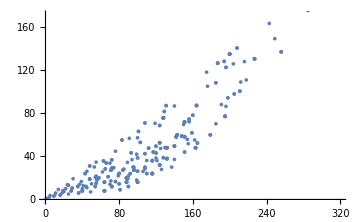

```mathematica
multFreeRings = Cases[ FRL, ring_ /; Mult[ring] == 1 ];
ListPlot[ 
	Table[ { NNZSC[ ring ], FPDim[ ring ] }, { ring, multFreeRings } ],
	"ImageSize" -> Medium
]
```

Colour the rings according to rank, add labels, and add tooltips

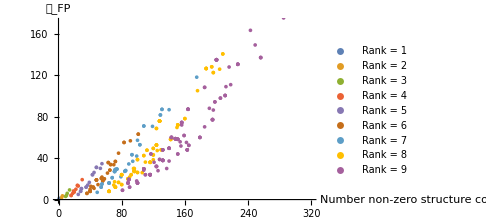

```mathematica
ListPlot[ 
	Table[ Tooltip[{ NNZSC[ ring ], FPDim[ ring ]}, FC[ring] ], { ring, # } ]& /@ GatherBy[ multFreeRings, Rank ],
	PlotLegends -> Table[ "Rank = " <> ToString[i], {i, Max[ Rank /@ multFreeRings ] } ], 
	AxesLabel->{ "Number\nnon-zero\nstructure\nconstants", "𝒟_FP" },
	ImageSize->Medium
]
```

## Working with Elements

You can call elements either by invoking ring[[el]] where el is either an integer denoting the i’th particle or 
it could be the name of the element itself. The product between two element is invoked by calling 
CenterDot[ ring[[el1]], ring[[el2]] ] or using the infix operator · ( Esc . Esc ).

Multiply two elements of the Ising fusion ring

```mathematica
r = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
	,
	"ElementNames"-> {"|01d7ed","ψ","σ"}
];

r[[ψ]]·r[[σ]]
```

σ

or

```mathematica
r[[2]]·r[[3]]
```

σ

or

```mathematica
CenterDot[ r[[2]], r[[3]] ]
```

σ

The product is associative and works for any number of elements

```mathematica
CenterDot[r[[3]],r[[3]],r[[1]]+r[[3]],r[[3]]+r[[2]]]
```

3 𝟭+3 ψ+4 σ

Calculations can entered in a more readable form using a Block statement

```mathematica
Block[{
	id = r[[1]],
	ψ  = r[[2]],
	σ  = r[[3]]
	},
	( 3 ψ + 2 σ + id )·ψ·( ψ + 3 id )
]
```

10 𝟭+6 ψ+8 σ

## Working with Fusion Categories

## Initializing a Fusion Category

### From the built-in list of fusion categories

Anyonica contains a built-in list of all multiplicity-free fusion categories up to rank 7. It can be accessed via FusionCategoryList (or FCL). The first 30 entries are obtained as follows

```mathematica
FusionCategoryList[[;;30]]
```

{FC[[Trivial]_(1,1)^1],FC[[SubscriptBox[ℤ, 2]]_(1,1)^1],FC[[SubscriptBox[ℤ, 2]]_(1,1)^2],FC[[SubscriptBox[ℤ, 2]]_(1,2)^1],FC[[SubscriptBox[ℤ, 2]]_(1,2)^2],FC[[SubscriptBox[ℤ, 2]]_(2,1)^1],FC[[SubscriptBox[ℤ, 2]]_(2,1)^2],FC[[SubscriptBox[ℤ, 2]]_(2,2)^1],FC[[SubscriptBox[ℤ, 2]]_(2,2)^2],FC[[Fib]_(1,1)^1],FC[[Fib]_(1,2)^1],FC[[Fib]_(2,1)^1],FC[[Fib]_(2,2)^1],FC[[Ising]_(1,1)^1],FC[[Ising]_(1,1)^2],FC[[Ising]_(1,2)^1],FC[[Ising]_(1,2)^2],FC[[Ising]_(1,3)^1],FC[[Ising]_(1,3)^2],FC[[Ising]_(1,4)^1],FC[[Ising]_(1,4)^2],FC[[Ising]_(2,1)^1],FC[[Ising]_(2,1)^2],FC[[Ising]_(2,2)^1],FC[[Ising]_(2,2)^2],FC[[Ising]_(2,3)^1],FC[[Ising]_(2,3)^2],FC[[Ising]_(2,4)^1],FC[[Ising]_(2,4)^2],FC[[Rep(SubscriptBox[D, 3])]_(1,1)^1]}

Anyonica uses the convention that a fusion category is determined by 3 pieces of data: the F-symbols, the R-symbols, and the pivotal structure. Two fusion categories C_1 and C_2 are considered equivalent if there exists a combination of a fusion ring automorphism and a gauge transform that maps the values of the F-symbols, R-symbols and pivotal structure of C_1 onto those of C_2. For example, there are 16 fusion categories belonging to the Ising fusion ring: there are two different sets of F-symbols and for each of those 4 different sets of R-symbols and for each of those 2 different sets of pivotal coefficients.

Just like for fusion rings, each fusion categories has a unique code attached to them. This can be obtained by evaluating FormalCode, e.g.

```mathematica
FormalCode @ FusionCategoryList[[13]]
```

{2,1,0,2,2,2,1}

The category can then later be obtained by using the FusionCategoryByCode function (or FRBC)

```mathematica
FusionCategoryByCode[ { 2, 1, 0, 2, 2, 2, 1 } ]
```

FC[[Fib]_(2,2)^1]

Typically it is desirable to find all fusion categories belonging to a certain fusion ring. This can be done using the FusionCategories function

```mathematica
isingRing = FRL[[4]];
FusionCategories[ isingRing ]
```

{FC[[Ising]_(1,1)^1],FC[[Ising]_(1,1)^2],FC[[Ising]_(1,2)^1],FC[[Ising]_(1,2)^2],FC[[Ising]_(1,3)^1],FC[[Ising]_(1,3)^2],FC[[Ising]_(1,4)^1],FC[[Ising]_(1,4)^2],FC[[Ising]_(2,1)^1],FC[[Ising]_(2,1)^2],FC[[Ising]_(2,2)^1],FC[[Ising]_(2,2)^2],FC[[Ising]_(2,3)^1],FC[[Ising]_(2,3)^2],FC[[Ising]_(2,4)^1],FC[[Ising]_(2,4)^2]}

### Manually

Manually initializing a fusion category is done by evaluating FusionCategory[ “FusionRing” -> ring, “FSymbols” -> fSymb, ... ]. For example, one of the ℤ_2 categories can be initialized as follows

```mathematica
z2Ring = FRL[[2]]
z2Fs = {ℱ[1,1,1,1,1,1]->1,ℱ[1,1,2,2,1,2]->1,ℱ[1,2,1,2,2,2]->1,ℱ[1,2,2,1,2,1]->1,ℱ[2,1,1,2,2,1]->1,ℱ[2,1,2,1,2,2]->1,ℱ[2,2,1,1,1,2]->1,ℱ[2,2,2,2,1,1]->-1};

z2Cat = FusionCategory[ "FusionRing" -> z2Ring, "FSymbols" -> z2Fs ]
```

FR[ℤ_2]

FC[2,1,0,1,_]

The function FusionCategory checks whether the data given is valid. This might cause issues for some fusion rings.

```mathematica
fibRing = FRL[[3]];
fibFs = {ℱ[1,1,1,1,1,1]->1,ℱ[1,1,2,2,1,2]->1,ℱ[1,2,1,2,2,2]->1,ℱ[1,2,2,1,2,1]->1,ℱ[1,2,2,2,2,2]->1,ℱ[2,1,1,2,2,1]->1,ℱ[2,1,2,1,2,2]->1,ℱ[2,1,2,2,2,2]->1,ℱ[2,2,1,1,1,2]->1,ℱ[2,2,1,2,2,2]->1,ℱ[2,2,2,1,2,2]->1,ℱ[2,2,2,2,1,1]->1/2 (-1+√5),ℱ[2,2,2,2,1,2]->√(1/2 (-1+√5)),ℱ[2,2,2,2,2,1]->√(1/2 (-1+√5)),ℱ[2,2,2,2,2,2]->1/2 (1-√5)};

fibCat = FusionCategory[ "FusionRing" -> fibRing, "FSymbols" -> fibFs ]
```

FusionCategory::invalidfsymbols: The F-symbols are not a valid solution to the pentagon equations. This might be due Mathematica being unable to simplify certain expressions. If so, use the option "PreEqualCheck" to force simplification. Invalid equations:
{√(1/2 (-1+√5))==1/4 (1-Power[«2»])^2 √(1/2 (-1+Power[«2»]))+(-1+√5)^(3/2)/(2 √2)}

FusionCategory::invaliddata: The data provided does not correspond to a fusion category.

FC[2,1,0,2,_]

As the warning message suggests, this problem can be resolved by giving an optional argument  “PreEqualCheck”

```mathematica
fibCat = FusionCategory[ "FusionRing" -> fibRing, "FSymbols" -> fibFs, "PreEqualCheck" -> RootReduce ]
```

FC[2,1,0,2,_]

If one is sure that the data is correct, then some time can be saved by skipping the validity check.

```mathematica
fibCat = FusionCategory[ "FusionRing" -> fibRing, "FSymbols" -> fibFs, "SkipCheck" -> True ]
```

FC[2,1,0,2,_]

The braided and pivotal structures are also part of the data of a FusionCategory object. They can be given with the options “RSymbols” and “PivotalStructure”

```mathematica
ct=FusionCategories[FRL[[3]]][[1]]
```

FC[[Fib]_(1,1)^1]

```mathematica
fibRs = {ℛ[1,1,1]->1,ℛ[1,2,2]->1,ℛ[2,1,2]->1,ℛ[2,2,1]->ⅇ^((4 ⅈ π)/5),ℛ[2,2,2]->-ⅇ^((2 ⅈ π)/5)};
fibPiv = {𝓅[1]->1,𝓅[2]->1};

fibCat = 
	FusionCategory[ 
		"FusionRing" -> fibRing, 
		"FSymbols" -> fibFs,
		"RSymbols" -> fibRs,
		"PivotalStructure" -> fibPiv,	 
		"SkipCheck" -> True 
	]
```

FC[2,1,0,2,_]

There are several other pieces of data that can be added to a category. The following is an example where (except for “SkipCheck”)  all possible options of the function FusionCategory are used

```mathematica
isingCat = 
	FusionCategory[ 
		"FusionRing" -> FRL[[4]],
		"FSymbols" -> {ℱ[1,1,1,1,1,1]->1,ℱ[1,1,2,2,1,2]->1,ℱ[1,1,3,3,1,3]->1,ℱ[1,2,1,2,2,2]->1,ℱ[1,2,2,1,2,1]->1,ℱ[1,2,3,3,2,3]->1,ℱ[1,3,1,3,3,3]->1,ℱ[1,3,2,3,3,3]->1,ℱ[1,3,3,1,3,1]->1,ℱ[1,3,3,2,3,2]->1,ℱ[2,1,1,2,2,1]->1,ℱ[2,1,2,1,2,2]->1,ℱ[2,1,3,3,2,3]->1,ℱ[2,2,1,1,1,2]->1,ℱ[2,2,2,2,1,1]->1,ℱ[2,2,3,3,1,3]->1,ℱ[2,3,1,3,3,3]->1,ℱ[2,3,2,3,3,3]->-1,ℱ[2,3,3,1,3,2]->-1,ℱ[2,3,3,2,3,1]->-1,ℱ[3,1,1,3,3,1]->1,ℱ[3,1,2,3,3,2]->1,ℱ[3,1,3,1,3,3]->1,ℱ[3,1,3,2,3,3]->1,ℱ[3,2,1,3,3,2]->1,ℱ[3,2,2,3,3,1]->1,ℱ[3,2,3,1,3,3]->1,ℱ[3,2,3,2,3,3]->-1,ℱ[3,3,1,1,1,3]->1,ℱ[3,3,1,2,2,3]->1,ℱ[3,3,2,1,2,3]->-1,ℱ[3,3,2,2,1,3]->-1,ℱ[3,3,3,3,1,1]->1/(√2),ℱ[3,3,3,3,1,2]->-1/(√2),ℱ[3,3,3,3,2,1]->-1/(√2),ℱ[3,3,3,3,2,2]->-1/(√2)},
		"RSymbols" -> {ℛ[1,1,1]->1,ℛ[1,2,2]->1,ℛ[1,3,3]->1,ℛ[2,1,2]->1,ℛ[2,2,1]->-1,ℛ[2,3,3]->-ⅈ,ℛ[3,1,3]->1,ℛ[3,2,3]->-ⅈ,ℛ[3,3,1]->ⅇ^((7 ⅈ π)/8),ℛ[3,3,2]->ⅇ^(-(5 ⅈ π)/8)},
		"PivotalStructure" ->  {𝓅[1]->1,𝓅[2]->1,𝓅[3]->-1},
		"Unitary" -> False,
		"FormalParameters" -> { 3, 1, 0, 1, 2, 3, 2 },
		"Twists" ->  {𝓉[1]->1,𝓉[2]->-1,𝓉[3]->(-1)^(1/8)},
		"SMatrix" -> {{1,1,-√2},{1,1,√2},{-√2,√2,0}},
		"Modular" -> True,
		"PreEqualCheck" -> RootReduce
	]
```

FC[[Ising]_(2,3)^2]

### Via constructions

In the future I hope to add constructions for the SU_2(k) and PSU_2(k) fusion categories.

## Categorifying Fusion Rings

### Obstructions to Categorification

Before attempting to categorify a fusion ring it might be interesting to apply one of the categorifiability criteria (see Classification of Grothendieck rings of complex fusion
categories of multiplicity one up to rank six, Zhengwei Liu · Sebastien Palcoux · Yunxiang Ren) . At the moment there are 5 built-in criteria. For all of these functions, except the CSPCValue, the value True indicates that the ring is not categorifiable. A negative number coming from the CSPCValue indicates that a ring has no unitary category.

```mathematica
TableForm @
Prepend[{ZSCriterion, CSPCValue, DNCriterion, PDCCriterion, LCriterion}] @
Table[ 
	{ ZSCriterion[r], CSPCValue[10][r], DNCriterion[r], PDCCriterion[r], LCriterion[r] },
	{ r, FRL[[;;30]] }
]
```

ZSCriterion | CSPCValue | DNCriterion | PDCCriterion | LCriterion
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | True | True | True
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | True | True | True
False | ∞ | False | False | False
False | ∞ | False | False | False
True | -0.96226071 | True | True | True
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | True | True | False
True | -0.53553391 | True | True | False
False | ∞ | False | False | False
False | ∞ | False | False | False
False | ∞ | True | True | True
False | ∞ | False | False | False

### Solving the Pentagon Equations

The function SolvePentagonEquations can be used to solve the pentagon equations for a fusion ring.

```mathematica
SolvePentagonEquations[ FRL[[2]] ]
```

{{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→1},{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→-1}}

The function returns all possible solutions, including non-unitary ones and solutions where some of the F-symbols are non-trivially 0.

For some fusion rings this function can take a lot of time or exhaust all the available memory. Therefore quite a number of optional arguments can be given to fine tune the process of solving these equations. To understand where these options are used it is interesting to know a little bit about what the function SolvePentagonEquations does behind the scene. 
When one evaluates SolvePentagonEquations the following steps are performed

The pentagon equations are set up with the assumption that vacuum F-symbols are 1. 
Main function(s) used: PentagonEquations

The gauge symmetries are reduced by demanding that no gauge transform is allowed to change vacuum F-symbols. 
Main function(s) used: RestrictMultiplicativeSymmetries

The possible combinations of F-symbols that can be zero are calculated.
Main function(s) used: FindZeroValues

The gauge symmetry is broken for the F-symbols that can never be zero.
Main function(s) used: BreakMultiplicativeSymmetry

Per set of zero values, the pentagon equations are updated and the gauge symmetry is broken to the extent possible.
Main function(s) used: BreakMultiplicativeSymmetry

The equations with two terms are solved, their solutions substituted, and the validity of each solution is checked. Invalid solutions are discarded. If the new system contains equations with two terms, this procedure is repeated until no systems exist with equations with two terms. 
Main function(s) used: ReduceByBinomials

The equations that are linear in one of the variables are used to reduce each system further. Often assumptions on the roots of some polynomials are added. Systems that are inconsistent are removed.
Main function(s) used: ReduceByLinearity

A Groebner basis is constructed for each system. Groebner bases that equal {1} are removed.
Main function(s) used: IncrementalGroebnerBasis

For each Groebner basis the roots are computed and only the valid solutions (i.e. invertible F-matrices and consistent with the assumptions added by ReduceByLinearity)
Main function(s) used: SolveUsingReduce

Each of the main functions comes with a list of options and many of those inherited by the SolvePentagonEquations function

SolvePentagonEquations inherits the following options from

FindZeroValues

“FindZerosBy”: The default “Logic” means that the system of pentagon equations is converted to a boolean proposition which is reduced via pattern  matching and use of logic. The function SatisfiabilityInstances then finds all booleans satisfying this proposition. Other options are “Reduce”, which uses the Reduce function instead of SatisfiabilityInstances to find all solutions, and “CCode” which creates, exports, compiles, runs specific CCode that finds solutions using a backtracking approach.

“SumSubsetParameter”: This option determined which fraction of the equations with more than two terms are used to find the zero values. The default is 0.3. This value does not affect the outcome of the function since at the end all solutions are tested for consistency by using all equations. The speed and memory consumption of the algorithm can be greatly affected by this option, however.

“SumSubsetFunction”: This option determines which equations with more than two terms are used to find zero values. By default the 30% with the lowest value of this option are used. The default is LeafCount, which provides a naive but efficient statistic of how complicated a polynomial is.

“InvertibleMatrices”: This option should not be set except for experimental reasons. It will become obsolete in the future.

BreakMultiplicativeSymmetry

“GaugeDemands”: By using “GaugeDemands” -> { ℱ[...] -> val_1, ..., ℱ[...] -> val_n } one can demand that certain F-symbols are gauged to specific values. BreakMultiplicativeSymmetry will try to choose a gauge such that these demands are satisfied in the order given. It might not be possible to satisfy all demands in which case a warning message is given and the impossible demands are ignored.

ReduceByBinomials

“StoreDecompositions”: Set to True if you want to store matrix decompositions that are used to solve subsystems of equations with only two terms. Solving these systems can be time consuming and this option allows to redo calculations without needing to solve these systems again. Since the stored data are matrix decompositions it is impossible to store incorrect solutions using this method.

“UseDatabaseOfSmithDecompositions”:  Set to True to use saved matrix decompositions.

ReduceByLinearity

“ReduceByLinearityMaxMemoryFactor”: Set to a number between 0 and 1 to constrain the maximum memory that can be used during the reduction via linear equations. The default is 0.9, which means that Mathematica calculates the memory available at the start of the algorithm and stops reducing systems when the memory threshold is reached.

“LinearReductionWeight”: Set to a function that determines the complexity of a linear equation a x + b == 0. The function should take two arguments: -b and a and return a number that increases with the complexity of a and b. The default function is RationalWeight, which is defined as follows:

```mathematica
RationalWeight[ num_, denom_ ] :=
Which[
MonomialQ[ num ] && MonomialQ[ denom ], 
{ 0, LeafCount @ Cancel[num/denom] },
MonomialQ[ denom ],
{ 1, LeafCount @ Cancel[num/denom] },
True,
{ 2, LeafCount @ denom }
];
```

IncrementalGroebnerBasis

“ReduceRoots”: Set to True if you want the function to apply RootReduce to coefficients of polynomials at various stages during the computation of the Groebner basis

“ReducePowerSums”: Set to True if you want to express roots of power sum polynomials by a value of the form e^a/b. If such roots appear then this is generically a good idea.

“Cutoff”: Set to a value between 0 and 1 to set the fraction of the number of simplest polynomials that should be used in each iteration of calculating the final Groebner basis. The default is 0.2.

“GroebnerWeightFunction”: Set to a function that determines the complexity of a polynomial. This is used when determining the subset of simplest polynomials, each iteration. The default is PolynomialDegree.

CoefficientDomain, “DegreeBound” → ∞, Method, Modulus, MonomialOrder, ParameterVariables, Sort, Tolerance: These are all inherited from the GroebnerBasis function and their effect can be found in the documentation of this function

Other options that affect the search for configurations of zero F-symbols are

“FindZerosUsingSums”: Set this to False if no equations with more than two terms should be used to find the zero values.

“NonSingular”: Set to True to assume that all F-symbols are non-zero.

“ZeroValues”: Set to a list of configurations of zero F-symbols. “ZeroValues” -> { { } } is equivalent to “NonSingular” -> True. Setting “ZeroValues” -> { { }, { ℱ[3,3,3,3,3,3] -> 0 } } tells the solver that there are two possible sets of zero values: one without zero values, and one where only the F-symbol ℱ[3,3,3,3,3,3] equals zero.

“UseDatabaseOfZeroValues”: Set to True to use a database of zero values. This database is initially empty but gets updated every time this option is set to True. The keys of the database are fusion rings and the values are lists of configurations of zero F-symbols. Note that this option should never be used when solving the pentagon equations with assumptions. The database does not store any assumptions so if the assumptions affect the possible zero values then later on, when one does not use assumptions, these values will still be used.

Some general options that are used for multiple other functions are

“PreEqualCheck”: Set to a function that will be applied to both sides of an equation before checking equality. Often decisions are made based on the consistency of some equations containing symbolic expressions. Mathematica does not simplify these by default and might not recognize that some equations (do not) hold. In this case on can set the PreEqualCheck option to a function that simplifies the equations before checking equality.

“SimplifyIntermediateResultsBy”: Set to a function that will be applied to symbolic numbers at various stages of calculation. This is mainly useful for functions that use recursion in combination with substitutions. By simplifying intermediate results the memory consumption typically gets reduced.

“Parallel”: Set to True to attempt to use parallel computation. This is experimental, though, since sometimes errors appear for which I find no cause or solution.

There is also the option to insert solutions for a sub ring via

“InjectSolution”: Set to a couple containing (1) a sub fusion ring of the ring whose pentagon equations should be solved, and (2) a correct solution to the pentagon equations of that sub fusion ring. One should not provide the embedding of the sub fusion ring into the ring since this is calculated automatically. The fusion ring itself suffices.

Lastly there is an experimental option “Equivalences” which should better be left alone at the moment.

Note: If in the following an option is not properly explain then it should be used with caution. In the future I hope to remove all redundant and experimental options

### Solving the Hexagon Equations

The function SolveHexagonEquations can be used to solve the hexagon equations for a fusion ring. It does not need solutions to the pentagon equations but a solution can be given by setting the “Knowns” option. The following code provides all solutions to the pentagon and hexagon equations for the ℤ_2 fusion ring. The R-symbols are automatically added to the known F-symbols.

```mathematica
z2Ring = FRL[[2]];
z2pentSol = SolvePentagonEquations[ z2Ring ]
z2hexSol = Table[ SolveHexagonEquations[ z2Ring, "Knowns" -> sol ], { sol, z2pentSol } ]
```

{{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→1},{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→-1}}

{{{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→1,ℛ[1,1,1]→1,ℛ[1,2,2]→1,ℛ[2,1,2]→1,ℛ[2,2,1]→1},{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→1,ℛ[1,1,1]→1,ℛ[1,2,2]→1,ℛ[2,1,2]→1,ℛ[2,2,1]→-1}},{{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→-1,ℛ[1,1,1]→1,ℛ[1,2,2]→1,ℛ[2,1,2]→1,ℛ[2,2,1]→ⅈ},{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,2,2,1,1]→-1,ℛ[1,1,1]→1,ℛ[1,2,2]→1,ℛ[2,1,2]→1,ℛ[2,2,1]→-ⅈ}}}

Note: At the moment there is no proper way to assume known values for the pentagon equations. Solving the hexagon equations first will thus only help to solve the pentagon equations if one manually tackles the pentagon equations. See the part on “Reducing Systems of Polynomial Equations” for functions that can help a lot with such an endeavour.

Besides the “Knowns” option, SolveHexagonEquations also has the “TwistFactors” option which can be set to a list of rational numbers { q_1, ..., q_r } for which { e^(2π ⅈ q_1), ..., e^(2π ⅈ q_n) } are the topological phases of the elements of the fusion ring. If such a list is given then the equations relating the topological twists and the R-symbols are added to the hexagon equations. This only makes sense if one assumes the category is spherical, though.

### Solving the Pivotal Equations

All possible pivotal structures of a fusion category can be found using the AllPivotalStructures function. This can either take a fusion ring and a set of F-symbols as follows

```mathematica
AllPivotalStructures[ z2Ring, z2pentSol[[1]] ]
```

{{𝓅[1]→1,𝓅[2]→-1},{𝓅[1]→1,𝓅[2]→1}}

or it can take a fusion category

```mathematica
z2Cat = FusionCategory[ "FusionRing" -> z2Ring, "FSymbols" -> z2pentSol[[1]] ];
AllPivotalStructures[ z2Cat ]
```

{{𝓅[1]→1,𝓅[2]→-1},{𝓅[1]→1,𝓅[2]→1}}

Note: the function AllPivotalStructures only cares about the F-symbols and the fusion ring. Even if the fusion category already has a specific pivotal structure, it will still return all possible pivotal structures compatible with the F-symbols. To get the pivotal structure of the category itself (if available) use the PivotalStructure function.

### Solving the Pivotal Equations

All possible pivotal structures of a fusion category can be found using the AllPivotalStructures function. This can either take a fusion ring and a set of F-symbols as follows

```mathematica
AllPivotalStructures[ z2Ring, z2pentSol[[1]] ]
```

{{𝓅[1]→1,𝓅[2]→-1},{𝓅[1]→1,𝓅[2]→1}}

or it can take a fusion category

```mathematica
z2Cat = FusionCategory[ "FusionRing" -> z2Ring, "FSymbols" -> z2pentSol[[1]] ];
AllPivotalStructures[ z2Cat ]
```

{{𝓅[1]→1,𝓅[2]→-1},{𝓅[1]→1,𝓅[2]→1}}

Note: the function AllPivotalStructures only cares about the F-symbols and the fusion ring. Even if the fusion category already has a specific pivotal structure, it will still return all possible pivotal structures compatible with the F-symbols. To get the pivotal structure of the category itself (if available) use the PivotalStructure function.

## Properties of Fusion Categories

### Standard Properties of Fusion Categories

#### Properties inherited from fusion rings

When applying any of the following functions

```mathematica
{
MultiplicationTable,MT,
SymbolicMultiplicationTable,SMT,
ElementNames,
AntiparticleMatrix,AM,
CommutativeQ,CQ,
Multiplicity,Mult,
MultiplicityFreeQ,MFQ,
NonZeroStructureConstants,NZSC,
NNonZeroStructureConstants,NNZSC,
Rank,
FrobeniusPerronDimensions,FPDims,
FrobeniusPerronDimension,FPDim,
NSelfDual,NSD,
NNonSelfDual,NNSD,
NSelfDualNonSelfDual,NSDNSD,
ConjugateCharge,CC,
InjectionForm
};
```

to a fusion category, it is automatically applied to the fusion ring belonging to that category.

#### Properties unique to fusion categories

Get the F-symbols of one of the Fibonacci fusion categories

```mathematica
fibCat = FCL[[13]]
FSymbols @ fibCat
```

FC[[Fib]_(2,2)^1]

{ℱ[1,1,1,1,1,1]→1,ℱ[1,1,2,2,1,2]→1,ℱ[1,2,1,2,2,2]→1,ℱ[1,2,2,1,2,1]→1,ℱ[1,2,2,2,2,2]→1,ℱ[2,1,1,2,2,1]→1,ℱ[2,1,2,1,2,2]→1,ℱ[2,1,2,2,2,2]→1,ℱ[2,2,1,1,1,2]→1,ℱ[2,2,1,2,2,2]→1,ℱ[2,2,2,1,2,2]→1,ℱ[2,2,2,2,1,1]→1/2 (-1-√5),ℱ[2,2,2,2,1,2]→√(1/2 (1+√5)),ℱ[2,2,2,2,2,1]→-√(1/2 (1+√5)),ℱ[2,2,2,2,2,2]→1/2 (1+√5)}

The variables for the F-symbols are denoted by ℱ[a, b, c,d,e,f] (where the script form of F is obtained via Esc scF Esc)

Get the R-symbols of the category

```mathematica
RSymbols @ fibCat
```

{ℛ[1,1,1]→1,ℛ[1,2,2]→1,ℛ[2,1,2]→1,ℛ[2,2,1]→ⅇ^(-(2 ⅈ π)/5),ℛ[2,2,2]→-ⅇ^((4 ⅈ π)/5)}

The variables for the R-symbols are denoted by ℛ[a,b,c] (where the script form of R is obtained via Esc scR Esc)

Get  the pivotal structure of the fusion category

```mathematica
PivotalStructure @ fibCat
```

{𝓅[1]→1,𝓅[2]→1}

The variables for the pivotal coefficients are denoted by 𝓅[i] (where the script form of p is obtained via Esc scp Esc)

Get  the  twists  of  the  fusion  category

```mathematica
Twists @ fibCat
```

{𝓉[1]→1,𝓉[2]→(-1)^(2/5)}

The variables for the twists are denoted by 𝓉[i] (where the script form of t is obtained via Esc sct Esc)

Get the quantum dimensions of the fusion category

```mathematica
QuantumDimensions @ fibCat
```

{𝒹[1]→1,𝒹[2]→2/(-1-√5)}

The variables for the dimensions are denoted by 𝒹 (where the script form of d is obtained via Esc scd Esc)

Check whether the category is spherical

```mathematica
SphericalQ @ fibCat
```

True

Since it is braided it must also be a ribbon fusion category

```mathematica
RibbonQ @ fibCat
```

True

Check whether the category is unitary

```mathematica
UnitaryQ @ fibCat
```

False

Check whether the category is modular

```mathematica
ModularQ @ fibCat
```

True

Get the S-matrix

```mathematica
SMatrix @ fibCat
```

{{1,1/2 (1-√5)},{1/2 (1-√5),-1}}

## Operations on Fusion Categories

Apply a gauge transform

```mathematica
ApplyGaugeTransform
```

Permute the simple objects

```mathematica
PermutedFusionCategory
```

In the future I hope to add at least the functionality to calculate the center of a fusion category and compute zestings

## Combining and Comparing Fusion Categories

Take a tensor product of two categories

```mathematica
TensorProduct
```

Check whether two fusion categories are equivalent

```mathematica
EquivalentFusionCategoriesQ
```

In the future I hope to add ad least the functionality to decompose fusion categories, construct twisted products, check Morita equivalence,

## Navigating the Database

Work in progress...

## Reducing Systems of Polynomial Equations

Work in progress...